plot D1 + D2 + D3  = n - 1, where n = 30

WolframAlphaQueryResults

```mathematica
RegionFunction -> Function[{x,y,z}, 0 ≤ z ≤ 1 + x + y &&  0 ≤ y ≤ z - y &&   0 ≤ x ≤ y - x]

Plot3D[29-x-y, {x, 0, 30}, {y, 0, 30},  Filling->Bottom,FillingStyle->Opacity[0.7],Mesh->None, AxesLabel->{x,y,z},RegionFunction -> Function[{x,y,z}, x ≥ 0 && y ≥ 0 && z ≥ 0]]
```

RegionFunction→Function[{x,y,z},0≤z≤1+x+y&&0≤y≤z-y&&0≤x≤y-x]

-Graphics3D-

```mathematica
Plot3D[29-x-y, {x, 0, 30}, {y, 0, 30},  Filling->Bottom,FillingStyle->Opacity[0.7],Mesh->None, AxesLabel->{x,y,z},RegionFunction -> Function[{x,y,z}, x ≥ 0 && y ≥ 0 &&z ≥ 0 && y ≥ x]]
```

-Graphics3D-

-Graphics3D-

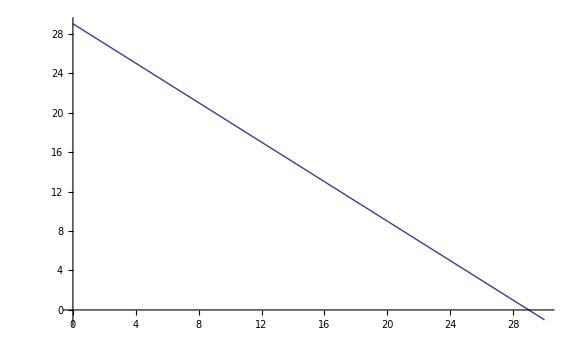

```mathematica
Plot[29 - x, {x, 0, 30}]
```